```mathematica
$IterationLimit=$RecursionLimit=50;
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"studiofunzioni.m"}]];
```

# Studio di funzioni: supporto all’insegnamento

## Sebastian Davrieux Francesco Trombi

## Introduzione

Il seguente notebook è stato creato con l’intento di fornire un supporto concreto all’insegnamento dell’analisi matematica, in particolare per quanto riguarda lo studio di funzioni, per docenti delle Scuole Secondarie Superiori.

Tale strumento, basato sul software Mathematica, fornirà dunque aiuti testuali e grafici, che mostrino agli studenti sia le motivazioni che determinano ogni passaggio dello studio di funzione, sia i risultati che tali passaggi comportano.
Questo strumento non vuole dunque porsi come una semplice “calcolatrice”, ma come complemento alle lezioni ed alle esercitazioni in classe.
Pertanto è richiesta la conoscenza dei concetti di base dell’analisi matematica, come equazioni, disequazioni, derivate, limiti, ecc.

## Studio di funzione

Innanzitutto è necessario definire la funzione che si desidera studiare, inserendola nell’apposito riquadro.
Note:
- la variabile deve essere x;
- dopo aver inserito la funzione nell’apposita cella premere Invio;
- il numero di Nepero (ⅇ) deve essere scritto in maiuscolo (E);
- logaritmo naturale di x si scrive Log[x];
- radice quadrata di x si scrive Sqrt[x];
- ricorda il ; alla fine della funzione.

```mathematica
Clear[f, x];
```

```mathematica
InputField[Dynamic[funzione]]
Dynamic[funzione]
Button["Calcola lo studio di funzione", FrontEndExecute[FrontEndToken[InputNotebook[],"EvaluateNotebook"]]]
```

Calcola lo studio di funzione

```mathematica
f[x_]:=funzione;
```

Studio del dominio

Il dominio è l’insieme di definizione di una funzione. In altre parole, definisce un sottoinsieme dello spazio in cui ha senso valutare la funzione. Nel suo calcolo è necessario tenere a mente che:
- se ci sono denominatori vanno posti diversi da zero;
- se ci sono logaritmi, i loro argomenti vanno posti strettamente maggiori di zero;
- se ci sono radici ad indice pari, i radicandi vanno posti maggiori o uguali a zero.

Una volta determinate tutte le condizioni, si mettono a sistema, poiché devono valere tutte contemporaneamente.

Ricorda: il dominio deve essere scritto nella forma di unione di intervalli.
Nota bene: con True si intende qualunque sia x appartenente ai numeri reali; con False si intende che la funzione non è definita nell’insieme dei numeri reali.

```mathematica
CalcolaDominio[f,x]
```

Non ci sono radici ad indice pari.

Non ci sono logaritmi da controllare

Il denominatore:

{-5+x}

Deve essere diverso di zero, quindi calcolo i valori per cui il denominatore è minore di zero e maggiore di zero e risulta:

{x>5,x<5}

Quindi facendo l'intersezione tra questi domini, il dominio è:

x<5||x>5

Studio di parità e disparità

Studiare la parità o la disparità di una funzione può rivelarsi estremamente utile, soprattutto in vista del disegno del grafico.
Se una funzione è pari, allora è simmetrica rispetto all’asse delle y.
Se una funzione è dispari, allora è simmetrica rispetto all’origine degli assi (0, 0).
In una di queste due eventualità il lavoro di disegno del grafico verrebbe dimezzato.

Una funzione f è pari se:
		f ( - x ) = f ( x );
una funzione f è dispari se:
		f ( - x ) = - f ( x ).
		
Ricorda: una funzione può essere pari o dispari o nessuna delle due.

```mathematica
ControlloPariDispari[f,x]
```

La funzione non è pari.

La funzione non è dispari.

Intersezione con gli assi

Un punto di riferimento utile al disegno finale del grafico può essere ricavato individuando i punti in cui la funzione interseca gli assi x e y.

### Intersezione con l’asse delle x

Per verificare le intersezioni tra la funzione e l’asse delle ascisse è innanzitutto necessario ricordare che l’equazione che individua tale asse è y = 0.
Essendo che y = f ( x ), per ricavare i possibili valori di intersezione sarà necessario risolvere l’equazione:
		f ( x ) = 0.

### Intersezione con l’asse delle y

Per verificare la presenza di un’intersezione tra la funzione e l’asse delle ordinate è necessario ricordare che l’equazione che individua tale asse è x = 0. 
Ponendo dunque x = 0, si calcola f ( 0 ); poi si risolve l’equazione:
		 y = f ( 0 ).

Ricorda: ci possono essere una, più o nessuna intersezione con l’asse delle ascisse, mentre ci possono essere o una o nessuna intersezione con l’asse delle ordinate.

```mathematica
ControlloIntersezioneAssi[f,x]
```

Per scoprire dove interseca l'asse x poniamo il numeratore = 0:

-1+2 x^2==0

che risulta:

x==-1/(√2)||x==1/(√2)

Per scoprire dove interseca l'asse y, calcoliamo f(x) con x=0 se il dominio lo ammette e otteniamo che interseca l'asse y in

y==-1

Studio del segno

Studiare il segno della funzione è utile nel disegno del grafico poiché permette di individuare gli intervalli del dominio in cui la funzione è positiva o negativa, dunque dove il grafico si trova al di sopra dell’asse delle ascisse e dove al di sotto.
Nelle intersezioni con l’asse delle x la funzione cambia ovviamente di segno.

Per conoscere il segno di una funzione f, basta risolvere la disequazione:
		f ( x ) > 0.
In questo modo tutti gli intervalli del dominio restituiti da questa disequazione sono quelli in cui la funzione è positiva (il cui grafico è dunque al di sopra dell’asse delle ascisse); i restanti intervalli del dominio rappresentano invece dove la funzione è negativa (il cui grafico è dunque al di sotto dell’asse delle ascisse).

Ricorda: le soluzioni da prendere in considerazione devono rientrare nel dominio della funzione.

```mathematica
SegnoFunzione[f,x]
```

La funzione è positiva per -1/(√2)<x<1/(√2)||x>5

Limiti agli estremi del dominio

Gli estremi del dominio sono tutti quei punti che delimitano un intervallo appartenente al dominio: in altre parole sono i “confini” del dominio della funzione.

I punti più interessanti da questo punto di vista sono quelli per cui la funzione non è definita: il comportamento della stessa andrà dunque studiato in un intorno di questi punti.
Un intorno è un insieme di punti vicini ad un punto (in questo caso un punto dove la funzione non è definita), leggermente distanti da esso. Esistono intorni sinistri, intorni destri oppure intorni completi.

Si prenda per esempio il punto x_1: un intorno sinistro del punto x_1 è, in pratica, un punto con ascissa x_1 - ε (dove ε è una quantità molto piccola), dunque un punto spostato a sinistra rispetto ad x_1; un intorno destro è definito dalla coordinata x_1 + ε, dunque leggermente spostato a destra rispetto ad x_1.

Se lo studio dei limiti agli estremi del dominio individua dei limiti tendenti ad infinito, è possibile cercare la presenza o l’assenza di asintoti verticali, orizzontali o obliqui.

```mathematica
CalcolaLimiti[f,x]
```

Gli estremi inferiori per il calcolo del limite sono:

{5}

e gli estremi superiori sono:

{5}

Il limite per x->-∞ nell'intorno destro = -∞ quindi è un asintoto verticale.

Il limite per x->∞ nell'intorno sinistro = ∞ quindi è un asintoto verticale.

Il limite per x->5 nell'intorno destro = ∞ quindi è un asintoto verticale.

Il limite per x->5 nell'intorno sinistro = -∞ quindi è un asintoto verticale.

Derivata prima, massimi e minimi, monotonia

Lo studio della derivata prima di una funzione permette di:
- comprendere in quali intervalli la funzione cresce (monotona crescente) ed in quali intervalli decresce (monotona decrescente);
- individuare i punti di massimo e di minimo, locali ed assoluti, della funzione, cioè i punti in cui la funzione primitiva cambia la monotonia.

Il primo passaggio consiste nel calcolo della funzione f ’ ( x ), cioè la deriva prima della funzione f; successivamente è necessario individuarne il dominio.

Il passo successivo consiste nello studio del segno, esattamente come visto in precedenza: applicato però alla derivata prima. È dunque necessario risolvere la disequazione:
	f ’ ( x ) ≥ 0.

Gli intervalli in cui la derivata prima è positiva (cioè con il grafico al di sopra dell’asse della ascisse) indicano che la funzione primitiva cresce in corrispondenza di essi; gli intervalli in cui la derivata è negativa (cioè con il grafico al di sotto dell’asse delle ascisse) indicano che la funzione primitiva decresce in corrispondenza di essi. 
I punti in cui la derivata prima si annulla saranno i candidati massimi o minimi della funzione f (detti anche punti estremanti della funzione).
Poniamo per esempio che x_1 sia uno di questi punti. x_1 è:
- punto di massimo, se la derivata è positiva prima di x_1 e negativa poi;
- punto di minimo, se la derivata è negativa prima di x_1 e positiva poi.

La derivata prima della funzione è:

(1-20 x+2 x^2)/(-5+x)^2

Le soluzioni della derivata prima sono:

{x→0.0502525}
{x→9.94975}

Gli intervalli in cui la derivata è positiva sono:

x<0.0502525||x>9.94975

Gli intervalli in cui la derivata è negativa sono:

0.0502525<x<5.||5.<x<9.94975

Il grafico della derivata prima è il seguente:

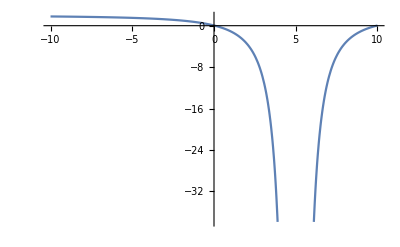

```mathematica
SegnoDerivataPrima[f,x]
```

Derivata seconda, convessità e punti di flesso

Lo studio della derivata seconda di una funzione permette di:
- comprendere in quali intervalli la funzione è convessa ed in quali è concava;
- individuare i punti di flesso, cioè i punti in cui la funzione primitiva cambia la concavità. 

Il primo passaggio consiste nel calcolo della funzione f ’’ ( x ), cioè la derivata seconda della funzione f (equivalente alla derivata prima della derivata prima di f); successivamente è necessario individuarne il dominio, considerando che alla fine quello che ci interesserà sarà l’unione dei domini della funzione primitiva, della derivata prima e della derivata seconda:
	Dom(f)∩Dom(f’)∩Dom(f’’).

Il passo successivo consiste nello studio del segno, esattamente come visto in precedenza: applicato però alla derivata seconda. È dunque necessario risolvere la disequazione:
		f ’’ ( x ) ≥ 0.
		
Gli intervalli in cui la derivata seconda è positiva (cioè con il grafico al di sopra dell’asse delle ascisse) indicano che la funzione primitiva è convessa in corrispondenza di essi; gli intervalli in cui la derivata seconda è negativa (cioè con il grafico al di sotto dell’asse delle ascisse) indicano che la funzione primitiva è concava in corrispondenza di essi.
I punti in cui la derivata si annulla saranno i candidati punti di flesso della funzione f.
Poniamo per esempio che x_1 sia uno di questi punti. x_1 è punto di flesso se:
- la derivata seconda è positiva prima di x_1 e negativa poi (dunque la funzione primitiva è convessa e poi concava);
- la derivata seconda è negativa prima di x_1 e positiva poi (dunque la funzione primitiva è concava e poi convessa).

Ricorda: tutti i punti x che risolvono l’equazione f ’’( x ) = 0 ma che non stanno nell’intersezione dei tre domini (Dom(f)∩Dom(f’)∩Dom(f’’)) non sono punti di flesso: è fondamentale capire che, anche se in certi punti si ha una variazione di convessità, ma in tali punti la funzione y = f ( x ) non è definita, essi non sono punti di flesso.

La derivata seconda è

4/(-5+x)-(8 x)/(-5+x)^2+(2 (-1+2 x^2))/(-5+x)^3

Non ci sono soluzioni per la derivata seconda.

Gli intervalli in cui la derivata seconda è positiva e dunque la funzione è convessa sono:

x>5.

Gli intervalli in cui la derivata seconda è negativa e dunque la funzione è concava sono:

x<5.

Il grafico della derivata seconda è il seguente:

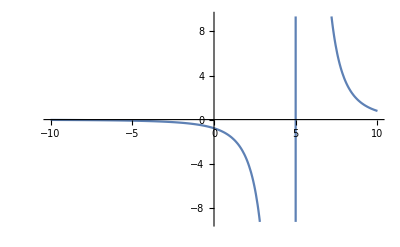

```mathematica
SegnoDerivataSeconda[f,x]
```

Grafico della funzione

Per disegnare correttamente il grafico della funzione in esame, è necessario riprendere tutte le informazioni ricavate nei vari passaggi precedenti a questo. Un buon modo per disegnarlo è procedere nel seguente modo:
1) disegnare gli assi cartesiani e le intersezioni che la funzione ha con essi;
2) prendendo gli intervalli risultati dal calcolo del segno della funzione, cancellare la zona di piano sotto l’asse x in corrispondenza degli intervalli in cui la funzione è positiva; cancellare poi la zona di piano sopra l’asse x in corrispondenza degli intervalli in cui la funzione è negativa;
3) tracciare gli eventuali asintoti (orizzontali, verticali ed obliqui), e disegnare una bozza del comportamento della funzione in loro prossimità;
4) segnare i punti di massimo e minimo individuati durante la fase di studio della derivata prima;
5) segnare i punti di flesso individuati durante la fase dello studio della derivata seconda;
6) disegnare il grafico, rispettando gli intervalli di monotonia crescente e decrescente (ricavati dallo studio della derivata prima) e rispettando gli intervalli di convessità e di concavità (ricavati dallo studio della derivata seconda).

Ricorda: il grafico di funzione indicato in seguito sarà preciso, poiché calcolato dal computer. Il tuo grafico potrà essere anche meno preciso, purché rispetti i vincoli definiti durante i vari passaggi.

Il grafico della funzione è:

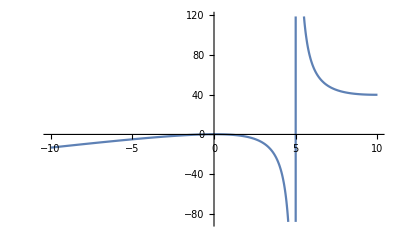

```mathematica
GraficoFunzione[f,x]
```

## Conclusioni

Il progetto presentato ha come scopo quello di essere un aiuto all’insegnamento degli argomenti centrali dell’analisi matematica, in particolare nelle scuole secondarie superiori.
Le descrizioni allegate ad ogni passaggio devono essere prese come un semplice accompagnamento, non adatto a sostituire le ore di lezione necessarie per assimilare i concetti utilizzati.
Pertanto è consigliato l’utilizzo di tale software solamente dopo aver affrontato insieme all’insegnante tutti gli argomenti necessari per svolgere uno studio di funzione.
In caso di funzione esponenziale sorgono dei problemi, poiché, per esempio, con una funzione del tipo ⅇ^(1/x) andrà a calcolare (grazie alle sostituzioni) 1/0.